```mathematica
meff2[s_]:=(m^2-(zh^2s^2*(mu-mu s)^2)/((1-s^3)L^2))
```

```mathematica
sol=Solve[D[meff2[s],s]==0&&0<s<1,s][[1]][[1]];
```

```mathematica
Simplify[s/.sol]//TeXForm
```

\frac{1}{3} \left(-2-\frac{2}{\sqrt[3]{37+9 \sqrt{17}}}+\sqrt[3]{37+9 \sqrt{17}}\right)

```mathematica
sol2=Solve[FullSimplify[ToRadicals[(meff2[s]/.sol)==-3^2/(4L^2)]],mu]
```

{{mu→-(√(-9-4 L^2 m^2))/(2 zh √Root[4+56 #1+24 #1^2+3 #1^3&,1])},{mu→(√(-9-4 L^2 m^2))/(2 zh √Root[4+56 #1+24 #1^2+3 #1^3&,1])}}

```mathematica
sol3=Sqrt[Simplify[ToRadicals[(mu/.sol2[[2]][[1]])^2]]]
```

1/2 √3 √(-(9+4 L^2 m^2)/((-8+(142-34 √17)^(1/3)+(142+34 √17)^(1/3)) zh^2))

```mathematica
sol3//TeXForm
```

\frac{1}{2} \sqrt{3} \sqrt{-\frac{4 L^2 m^2+9}{\left(-8+\sqrt[3]{142-34
   \sqrt{17}}+\sqrt[3]{142+34 \sqrt{17}}\right) \text{zh}^2}}

```mathematica
(sol3//.{m^2->-2/L^2,zh->3/(4π )})//N
```

7.71285

```mathematica
nsol=mu->17.02204449*3/(4π zh);
```

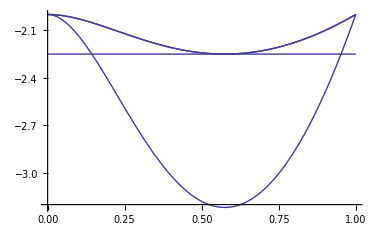

```mathematica
Plot[Table[((meff2[s]/.so)L^2)//.{m^2->-2/L^2,zh->3/(4π )},{so,{sol2,nsol}}]~Join~{-9/4},{s,0,1}]
```